# PeterBurbery/UndirectedGraphs

Functions for undirected graphs

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"Documentation"

"English"

"Guides"

"GraphFunctions.nb"Documentation/English/Guides/GraphFunctions.nb

"ReferencePages"

"Symbols"

"GeneralizedGraphData.nb"Documentation/English/ReferencePages/Symbols/GeneralizedGraphData.nb

"Girth.nb"Documentation/English/ReferencePages/Symbols/Girth.nb

"GraphConvexHull.nb"Documentation/English/ReferencePages/Symbols/GraphConvexHull.nb

"GraphicalDegreeSequenceQ.nb"Documentation/English/ReferencePages/Symbols/GraphicalDegreeSequenceQ.nb

"GraphPredicateData.nb"Documentation/English/ReferencePages/Symbols/GraphPredicateData.nb

"OddNodes.nb"Documentation/English/ReferencePages/Symbols/OddNodes.nb

"RandomCustomGraph.nb"Documentation/English/ReferencePages/Symbols/RandomCustomGraph.nb

"ResistanceMatrix.nb"Documentation/English/ReferencePages/Symbols/ResistanceMatrix.nb

"TakeLargestGraphComponentBy.nb"Documentation/English/ReferencePages/Symbols/TakeLargestGraphComponentBy.nb

"Tutorials"

"Kernel"

"UndirectedGraphs.wl"Kernel/UndirectedGraphs.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

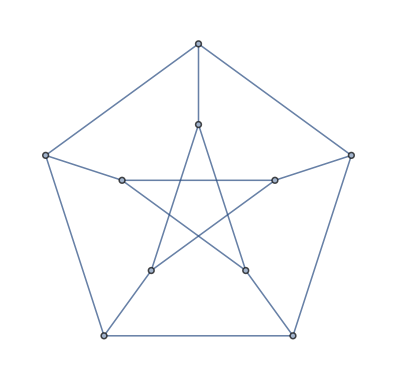

### Basic Description

Functions for undirected graphs.

### Details

Additional information about the paclet.

### Main Guide Page

File["C:\Users\peter\Documents\GitHub\undirected-graphs-paclet\Undirected Graphs\Documentation\English\Guides\GraphFunctions.nb"]

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Find the girth for the Petersen graph:

```mathematica
Girth[PetersenGraph[]]
```

5

Find graph data for the Petersen graph:

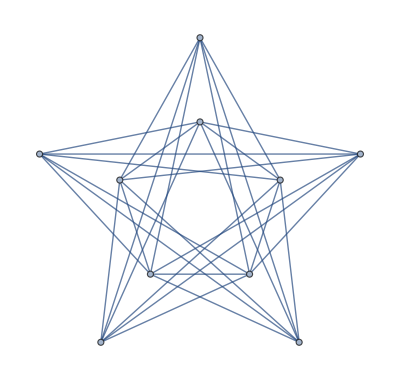
<|IncidenceMatrix→SparseArray[…],Order→10,Size→15,Nodes→{1,2,3,4,5,6,7,8,9,10},Edges→{1<->3,1<->4,1<->6,2<->4,2<->5,2<->7,3<->5,3<->8,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10},AdjacencyMatrix→SparseArray[…],GraphComplement→-Graphics-,GraphCenter→{1,2,3,4,5,6,7,8,9,10},GraphRadius→2,GraphDiameter→{1,2,3,4,5,6,7,8,9,10},GraphPeriphery→2|>

```mathematica
GeneralizedGraphData[PetersenGraph[]]
```

### Scope

## Source & Additional Information

### Creator

Peter Cullen Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/undirected-graphs-paclet/tree/main/Undirected%20Graphs

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Graph theory

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

EulerizeGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies <+$Path+>, <+Directory+>, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public <+ResourceObject+> content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of <+SystemCredential+>Click for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via <+ExternalEvaluate+>
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.